```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0 && Element[k,Integers] && k>0
```

r>0&&m∈Integers&&n∈Integers&&s>0&&k∈Integers&&k>0

```mathematica
f[r_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}}-0*IdentityMatrix[2]*I*r^p;f[r]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

```mathematica
En=E0+I*Ga;En=.
```

```mathematica
u={a[n]*x^(2*n),b[n]*x^(2*n+1)}*x^s
```

{x^(2 n+s) a[n],x^(1+2 n+s) b[n]}

```mathematica
p=2;
```

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[(D[u,x]-r'[x]*f[r[x]].u)*x^(-s+1)]]],{x^n,a[n],b[n]}];
g1//MatrixForm
```

(x^(2 n) ((1-m+2 n+s) a[n]+(-ⅈ En x^2+ⅈ x^4) b[n])
x^(2 n) ((-ⅈ En x+ⅈ x^3) a[n]+(x+m x+2 n x+s x) b[n]))

```mathematica
s=-1+m;
```

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,10}]/.x->0],{n2,0,10}];g2//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
a[0]=1; b[0]=ⅈ En a[0]/2/m;a[1]=ⅈ En b[0]/2;
```

```mathematica
a[0]=1; b[0]=ⅈ En a[0]/2/m;a[1]=ⅈ En b[0]/2;
b[n_]:=I*(En*a[n]-a[n-1])/2/(n+m);
a[n_]:=Simplify[I*(En b[n-1]-b[n-2])/2/n]
```

```mathematica
a[1]
```

-En^2/8

```mathematica
m=2;
```

```mathematica
En=.
```

```mathematica
Un[En_,m_,nN_,x_]:=Module[{n,U},
U={1};AppendTo[U,-En^2/(4 m)];AppendTo[U,(En (4+En^3+8 m))/(32 m (1+m))];G={ⅈ En /2/m};

For[n=3,n<nN,n++,
AppendTo[U,-((-1+m+n) U[[-2+n]]+En ((3-2 m-2 n) U[[-1+n]]+En (-2+m+n)U[[n]]))/(4 n (-2+m+n) (-1+m+n))];
];
({1,ⅈ En /2/m*x}+Sum[{U[[n+1]]*x^(2*n),I*(En*U[[n+1]]-U[[n]])/2/(n+m)*x^(2*n+1)},{n,1,nN-1} ])*x^(-1+m)//N]
```

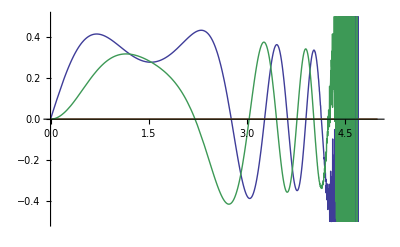

```mathematica
G={Re[#],Im[#]}&[Un[3,2,150,x]];Plot[G,{x,0,5},PlotRange->{-0.5,0.5}]
```

```mathematica
s
```

# RungeKutta von Links

```mathematica
Exit[]
```

```mathematica
U[En_,m_,g_,X_]:=Module[{n=10,U,G},
U=Un[En,m,n,X];G=-Un[En,m,n+1,X];
While[Sqrt[Abs[Conjugate[U-G].(U-G)]]>g,
n++;
U=G;G=-Un[En,m,n+1,X];

];
Print[n];
{Un[En,m,n,X],n}]
```

```mathematica
p=2;En=.
```

```mathematica
f[r_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}};f[rr]//MatrixForm
```

((-1+m)/rr | ⅈ (En-rr^2)
ⅈ (En-rr^2) | -m/rr)

```mathematica
k=U[En,m,10^-10,r][[1]];AppendTo[kK,{ }];
```

$Aborted

16

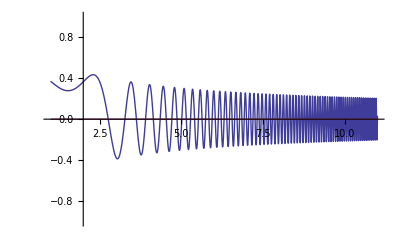

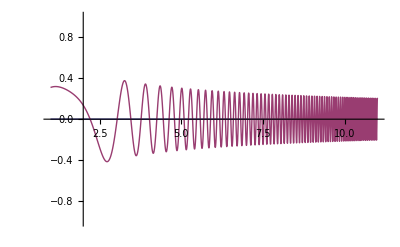

```mathematica
n=5000;S=1;h=10/n;ra=1;En=3;m=2;r=1;k=U[En,m,10^-10,r][[1]];
kK={{r,k}};
Do[
k0=h*f[r].k;k1=h*f[r+h/2].(k+k0/2);k2=h*f[r+h/2].(k+k1/2);k3=h*f[r+h].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{n}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;n]]//N}],PlotRange->{-ra,ra},Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;n]]//N}],PlotRange->{-ra,ra},Joined->True]

m=.;r=.;
```

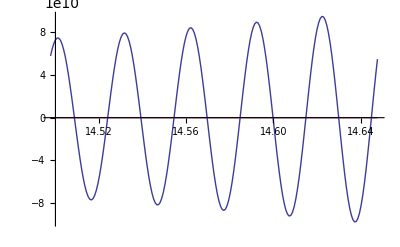

```mathematica
S=18000;n=200;ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],0*Im[#[[2,2]]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->True]
```

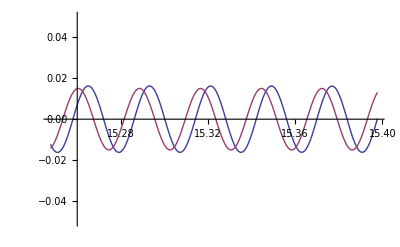

```mathematica
S=19000;n=200;ListPlot[Join[{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;S+n]]},{ {#[[1]],-0.1*Sin[(-#^3/3+10*#)]&[#[[1]]]*0.15}&/@kK[[S;;S+n]]}],PlotRange->{-ra,ra},Joined->True]
```

```mathematica
V={{1,-1},{1,1}}
```

```mathematica
{{1,-1},{1,1}}.{F[x],g[x]}
```

```mathematica
Inverse[V].{C1,C2}
```

{C1/2+C2/2,-C1/2+C2/2}

```mathematica
Expand[V.f[r].Inverse[V]]//MatrixForm
```

(-ⅈ En-1/(2 r)+ⅈ r^2 | -1/(2 r)+m/r
-1/(2 r)+m/r | ⅈ En-1/(2 r)-ⅈ r^2)

```mathematica
Finden und Einsetzen des Randverhaltens
```

```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0 && Element[k,Integers] && k>0
```

r>0&&m∈Integers&&n∈Integers&&s>0&&k∈Integers&&k>0

```mathematica
f[r_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}}-0*IdentityMatrix[2]*I*r^p;f[r]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

```mathematica
En=E0+I*Ga;En=.
```

```mathematica
u={Exp[I*(F1[x])]+Exp[I*F2[x]],Exp[I*(G1[x])]+Exp[I*G2[x]]}*x^s
```

{(ⅇ^(ⅈ F1[x])+ⅇ^(ⅈ F2[x])) x^(-1+m),(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x])) x^(-1+m)}

```mathematica
s=m-1
```

-1+m

```mathematica
p=2;
```

```mathematica
r[x_]:=x;
```

```mathematica
g1=-Collect[Expand[Simplify[Expand[(D[u,x]-r'[x]*f[r[x]].u)*F1[x]/u/I]]],{x^n,a[n],b[n]}]
```

{(5 ⅇ^(ⅈ G1[x]) F1[x])/(ⅇ^(ⅈ F1[x])+ⅇ^(ⅈ F2[x]))+(5 ⅇ^(ⅈ G2[x]) F1[x])/(ⅇ^(ⅈ F1[x])+ⅇ^(ⅈ F2[x]))-x^2 ((ⅇ^(ⅈ G1[x]) F1[x])/(ⅇ^(ⅈ F1[x])+ⅇ^(ⅈ F2[x]))+(ⅇ^(ⅈ G2[x]) F1[x])/(ⅇ^(ⅈ F1[x])+ⅇ^(ⅈ F2[x])))-(ⅇ^(ⅈ F1[x]) F1[x] F1'[x])/(ⅇ^(ⅈ F1[x])+ⅇ^(ⅈ F2[x]))-(ⅇ^(ⅈ F2[x]) F1[x] F2'[x])/(ⅇ^(ⅈ F1[x])+ⅇ^(ⅈ F2[x])),(5 ⅇ^(ⅈ F1[x]) F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))+(5 ⅇ^(ⅈ F2[x]) F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))-x^2 ((ⅇ^(ⅈ F1[x]) F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))+(ⅇ^(ⅈ F2[x]) F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x])))-((ⅈ ⅇ^(ⅈ G1[x]) F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))+(ⅈ ⅇ^(ⅈ G2[x]) F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))-(2 ⅈ ⅇ^(ⅈ G1[x]) m F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))-(2 ⅈ ⅇ^(ⅈ G2[x]) m F1[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x])))/x-(ⅇ^(ⅈ G1[x]) F1[x] G1'[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))-(ⅇ^(ⅈ G2[x]) F1[x] G2'[x])/(ⅇ^(ⅈ G1[x])+ⅇ^(ⅈ G2[x]))}

```mathematica
s=-1+m;
```

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,10}]/.x->0],{n2,0,10}];g2//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

# RungeKutta von Rechts

```mathematica
Exit[]
```

```mathematica
U[En_,m_,g_,X_]:=Module[{n=10,U,G},
U=Un[En,m,n,X];G=-Un[En,m,n+1,X];
While[Sqrt[Abs[Conjugate[U-G].(U-G)]]>g,
n++;
U=G;G=-Un[En,m,n+1,X];

];
Print[n];
{Un[En,m,n,X],n}]
```

```mathematica
p=2;En=.
```

```mathematica
f[r_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}};f[rr]//MatrixForm
```

((-1+m)/rr | ⅈ (3-rr^2)
ⅈ (3-rr^2) | -m/rr)

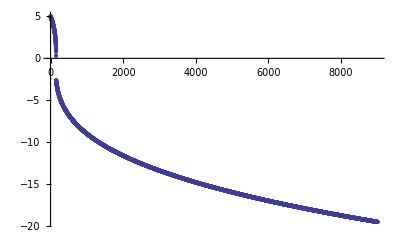

```mathematica
r=5//N;k={r};Do[
r-=0.28/r^2;AppendTo[k,r]
,{9000}];r=.;ListPlot[k]
```

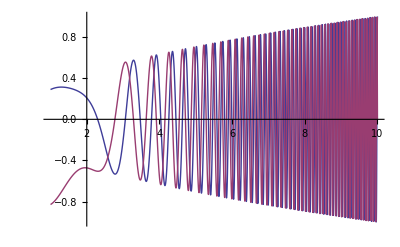

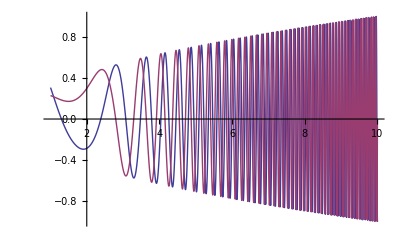

```mathematica
n=3000;S=1;ra=0.05;En=3;m=2;r=10//N;h=9/n;k={1,-1};
kK={{r,k}};
Do[
k0=h*f[r].k;k1=h*f[r+h/2].(k+k0/2);k2=h*f[r+h/2].(k+k1/2);k3=h*f[r+h].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r-=h;
AppendTo[kK,{r,k}],{n}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]
r=.;
```

1.

19

{-0.0989079,0.+0.0687335 ⅈ}

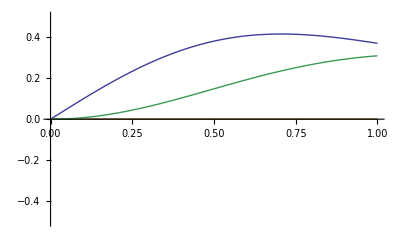

```mathematica
r=1//N
k=U[En,2,10^-10,r][[2]];Un[En,2,k,1]
G={Re[#],Im[#]}&[Un[3,2,k,x]];Plot[G,{x,0,r},PlotRange->{-0.5,0.5}]
r=.
```

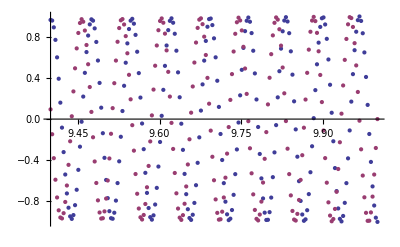

```mathematica
S=1;n=200;ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->False]
```

```mathematica
S=19000;n=200;ListPlot[Join[{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;S+n]]},{ {#[[1]],-0.1*Sin[(-#^3/3+10*#)]&[#[[1]]]*0.15}&/@kK[[S;;S+n]]}],PlotRange->{-ra,ra},Joined->True]
```

-Graphics-

```mathematica
V={{1,-1},{1,1}}
```

```mathematica
{{1,-1},{1,1}}.{F[x],g[x]}
```

```mathematica
Inverse[V].{C1,C2}
```

{C1/2+C2/2,-C1/2+C2/2}

```mathematica
Expand[V.f[r].Inverse[V]]//MatrixForm
```

(-ⅈ En-1/(2 r)+ⅈ r^2 | -1/(2 r)+m/r
-1/(2 r)+m/r | ⅈ En-1/(2 r)-ⅈ r^2)

```mathematica
Nullstellensuche
```

```mathematica
n=3000;S=1;ra=0.05;En=5;m=2;r=10//N;h=9/n;k={1,-1};
Do[
k0=h*f[r].k;k1=h*f[r+h/2].(k+k0/2);k2=h*f[r+h/2].(k+k1/2);k3=h*f[r+h].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r-=h;
,{n}];
Erg=k-Un[En,m,U[En,m,10^-10,1][[2]],1]
```

19

{0.273782-0.220723 ⅈ,-0.422103+0.0503209 ⅈ}

```mathematica
D[f[R],En]
```

General::ivar: 5 is not a valid variable.

∂_5 {{1/R,ⅈ (5-R^2)},{ⅈ (5-R^2),-2/R}}

```mathematica
r=1//N
k=U[En,2,10^-10,r][[2]];Un[En,2,k,1]
G={Re[#],Im[#]}&[Un[3,2,k,x]];Plot[G,{x,0,r},PlotRange->{-0.5,0.5}]
r=.
```

1.

19

{-0.0989079,0.+0.0687335 ⅈ}

-Graphics-

# RungeKutta von Links mit Randverhalten

```mathematica
Exit[]
```

```mathematica
U[En_,m_,g_,X_]:=Module[{n=10,U,G},
U=Un[En,m,n,X];G=-Un[En,m,n+1,X];
While[Sqrt[Abs[Conjugate[U-G].(U-G)]]>g,
n++;
U=G;G=-Un[En,m,n+1,X];

];
Print[n];
{Un[En,m,n,X],n}]
```

```mathematica
p=2;
```

```mathematica
f[u_,x_]:={ⅇ^(-ⅈ F[x]+ⅈ G[x]) En-ⅇ^(-ⅈ F[x]+ⅈ G[x]) x^2,ⅇ^(ⅈ F[x]-ⅈ G[x]) En-ⅈ/x+(2 ⅈ m)/x-ⅇ^(ⅈ F[x]-ⅈ G[x]) x^2}/.F[x]->u[[1]]/.G[x]->u[[2]];f[{F[x],G[x]},r]//MatrixForm
```

(ⅇ^(-ⅈ F[x]+ⅈ G[x]) En-ⅇ^(-ⅈ F[x]+ⅈ G[x]) r^2
ⅇ^(ⅈ F[x]-ⅈ G[x]) En-ⅈ/r+(2 ⅈ m)/r-ⅇ^(ⅈ F[x]-ⅈ G[x]) r^2)

```mathematica
n=5000;S=1;h=10/n;ra=0.05;En=5;m=2;r=0.1;k=Log[U[En,m,10^-25,r][[1]]/r^s]/I
kK={{r,k}};
Do[
k0=h*f[k,r];k1=h*f[(k+k0/2),r+h/2];k2=h*f[(k+k1/2),r+h/2];k3=h*f[(k+k2),r+h];
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{n}];ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;n]]//N},{ {#[[1]],0*Im[#[[2,1]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;n]]//N},{ {#[[1]],0*Im[#[[2,2]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]

m=.;r=.;
```

11

{0.0313618 ⅈ,1.5708+2.10163 ⅈ}

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

$Aborted

Part::take: Cannot take positions 1 through 5000 in {{0.1, {0.0313618\ ⅈ, 1.5708  + 2.10163\ ⅈ}}, « 9 », « 3501 »}.

Part::partd: Part specification (1 ;; 5000) ⟦ 2, 2 ⟧ is longer than depth of object.

Part::pspec: Part specification {1, Re[(1 ;; 5000) ⟦ 2, 2 ⟧]} is neither an integer nor a list of integers.

Part::partd: Part specification (1 ;; 5000) ⟦ 2, 2 ⟧ is longer than depth of object.

Part::pspec: Part specification {1, Re[(1 ;; 5000) ⟦ 2, 2 ⟧]} is neither an integer nor a list of integers.

Part::take: Cannot take positions 1 through 5000 in {{0.1, {0.0313618\ ⅈ, 1.5708  + 2.10163\ ⅈ}}, « 9 », « 3501 »}.

Part::partd: Part specification (1 ;; 5000) ⟦ 2, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

-Graphics-

```mathematica
3
```

```mathematica
Sqrt[5]//N
```

2.23607

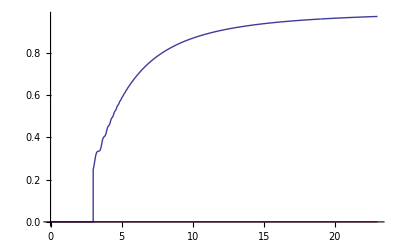

```mathematica
S=1;n=10000;ListPlot[Join[{ {#[[1]],Re[#[[2,1]]/(#[[1]]^3/3)]}&/@kK[[S;;S+n]]},{ {#[[1]],0*Im[#[[2,1]]]}&/@kK[[S;;S+n]]}],PlotRange->All,Joined->True]
```

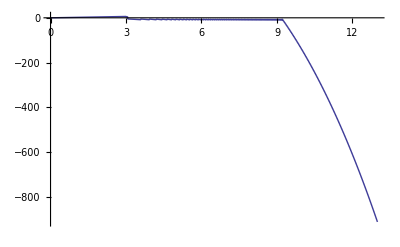

```mathematica
S=1;n=5000;ListPlot[Join[{ {#[[1]],Re[#[[2,2]]-(#[[1]]^3/3-En*#[[1]])]}&/@kK[[S;;S+n]]}],PlotRange->All,Joined->True]
```

```mathematica
En
```

5+0.2 ⅈ

```mathematica
S=19000;n=200;ListPlot[Join[{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;S+n]]},{ {#[[1]],-0.1*Sin[(-#^3/3+10*#)]&[#[[1]]]*0.15}&/@kK[[S;;S+n]]}],PlotRange->{-ra,ra},Joined->True]
```

-Graphics-

# RungeKutta von Rechts->Nullstellengesuche

```mathematica
Exit[]
```

```mathematica
p=2;
```

```mathematica
f[r_,En_,m_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}}-IdentityMatrix[2]*I*r^p;
```

{2.19637-1.69195 ⅈ,0.0535395+0.0697368 ⅈ}

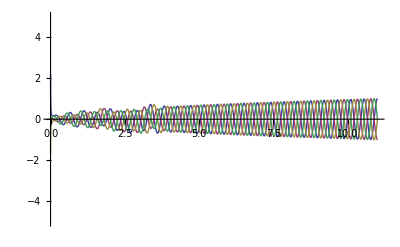

```mathematica
n=3000;En=14+I*0.001;m=2;r=11.0;h=r/(n-1);k={1,-1};
kK={{r,k}};
Do[
k0=h*f[r,En,m].k;k1=h*f[r+h/2,En,m].(k+k0/2);k2=h*f[r+h/2,En,m].(k+k1/2);k3=h*f[r+h,En,m].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r-=h;
AppendTo[kK,{r,k}],{n}];
Print[kK[[n,2]]];
ListPlot[Join[Table[ {#[[1]],Re[#[[2,i]]]}&/@kK[[1;;n]]//N,{i,2}],Table[ {#[[1]],Im[#[[2,i]]]}&/@kK[[1;;n]]//N,{i,2}]],PlotRange->{-5,5},Joined->True]
```

```mathematica
d[En_,m_,x_,X_,n_]:=Module[{k,k0,k1,k2,k3,k4},
r=X;h=(X-x)/(n);k={1,-1};
Do[
k0=h*f[r,En,m].k;k1=h*f[r+h/2,En,m].(k+k0/2);k2=h*f[r+h/2,En,m].(k+k1/2);k3=h*f[r+h,En,m].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r-=h;,{n}];
k4=k;
r=0.001;h=(X-x-r)/(n);k=U[En,m,0.001,r][[1]]*{1,-1}*ⅇ^((ⅈ r^3)/3);

Do[
k0=h*f[r,En,m].k;k1=h*f[r+h/2,En,m].(k+k0/2);k2=h*f[r+h/2,En,m].(k+k1/2);k3=h*f[r+h,En,m].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;,{n}];
k-k4
]
```

```mathematica
d[7,2,2,11.0,3000]
```

{-21.3966+38.1887 ⅈ,8.2075+3.56692 ⅈ}

```mathematica
AA=Table[Abs[d[i+I*j,2,2.0,11.0,3000][[1]]],{j,8,20,2},{i,0,5}]
```

{{2.01539×10^72,1.70761×10^71,2.23889×10^69,3.61115×10^68,4.14497×10^66,5.36746×10^65},{3.36981×10^79,8.41473×10^77,2.13402×10^76,4.93856×10^74,1.72678×10^73,4.46675×10^71},{4.80477×10^86,1.27969×10^85,3.48353×10^83,9.67405×10^81,2.79312×10^80,8.22132×10^78},{6.07865×10^93,1.78739×10^92,5.38671×10^90,1.66212×10^89,5.26181×10^87,1.70489×10^86},{6.97571×10^100,2.27062×10^99,7.57069×10^97,2.58576×10^96,9.04737×10^94,3.24291×10^93},{7.27266×10^107,2.62014×10^106,9.66553×10^104,3.65111×10^103,1.41238×10^102,5.59539×10^100},{6.89962×10^114,2.75055×10^113,1.12233×10^112,4.68769×10^110,2.00434×10^109,8.7738×10^107}}

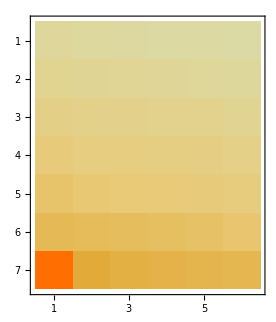

```mathematica
MatrixPlot[AA]
```